```mathematica
(*Setting options for figure plotting*)
```

```mathematica
th = 0.005;
SetOptions[Plot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,PointSize[th]}, PlotRange->All];
SetOptions[ListLogPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,PointSize[th]}, PlotRange->All];
SetOptions[ListLinePlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ParametricPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPointPlot3D, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[MatrixPlot, BaseStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->16]];
```

```mathematica
(*Process bnl data and generate synthetic data*)
```

```mathematica
ClearAll["Global`*"]

positionDirectory = FileNameJoin[{NotebookDirectory[],  "Raw Positions"}];
resultDirectory = FileNameJoin[{NotebookDirectory[], "RunResults"}];

fgfResultDirectory = FileNameJoin[{NotebookDirectory[], "Results"}];

fgfDirectory = FileNameJoin[{NotebookDirectory[], "Raw Data"}];

fgfSaveDirectory = FileNameJoin[{NotebookDirectory[], "fgfData"}];

smoothCurvatureDirectory = FileNameJoin[{NotebookDirectory[], "Curvatures"}];

syntheticDirectory =  FileNameJoin[{NotebookDirectory[], "SyntheticData"}];

SetDirectory[positionDirectory];


fileNames = StringTake[FileNames[], {1, -5}];
fileNames = {fileNames[[;;37]], fileNames[[82;;]], fileNames[[38;;81]]}//Flatten;


numFiles = Length[fileNames]



SetDirectory[fgfDirectory];
allProfiles = Import["AllProfiles.csv"];

nameList = DeleteDuplicates[allProfiles[[2;;,6]]];

numOfFGFs = nameList//Length;


smoothing = 0.2;

fgfData[index_] :=( 

fname = nameList[[index]];

profile = Pick[allProfiles[[2;;,{3,4}]], # == fname&/@ allProfiles[[2;;,6]]];

length =profile[[;;,1]]//N;
smoothedFGF = LowpassFilter[profile[[;;,2]] ,smoothing];

{ (length - Min[length])/(Max[length] - Min[length]), (smoothedFGF - Min[smoothedFGF])/(Max[smoothedFGF] - Min[smoothedFGF])}//Transpose

)


exportFGFData[index_] :=(
fData = fgfData[index];
fname = nameList[[index]];

If[StringContainsQ[fname, "VirginFemale"], fname = "V" <> fname];
If[StringContainsQ[fname, "VirginMale"], fname = "M" <> fname];

SetDirectory[fgfSaveDirectory];
Export[fname <> ".csv", fData]

)


plotFGF[index_] :=( 

fdata= fgfData[index] ;

ListLinePlot[fdata,AxesOrigin->{0,0}, AxesLabel->{"s", "fgf"},(*ColorFunction->Function[{x,y},ColorData["DeepSeaColors"][x]],*)PlotStyle->Green,LabelStyle->Directive[Bold, FontSize-> 18, Black]]

)


makeSynthenticData[index_]:= (

fname = nameList[[index]];

profile = Pick[allProfiles[[2;;,{3,4}]], # == fname&/@ allProfiles[[2;;,6]]];

length =profile[[;;,1]];
dataLength = Length[length];


synProc = EstimatedProcess[profile[[;;,2]], ARProcess[{a,b,c}, v]];
generated =RandomFunction[synProc, {1,dataLength}]["Paths"][[1,;;,2]];



smoothedFGF = LowpassFilter[generated,smoothing];

{ (length - Min[length])/(Max[length] - Min[length]), (smoothedFGF - Min[smoothedFGF])/(Max[smoothedFGF] - Min[smoothedFGF])}//Transpose

)


brownNoise[numPoints_]:= (
ResourceFunction["ColoredNoise"][numPoints, "Brown"]
)
makeSynthenticData2[index_]:= (

fname = nameList[[index]];

profile = Pick[allProfiles[[2;;,{3,4}]], # == fname&/@ allProfiles[[2;;,6]]];

length =profile[[;;,1]];
dataLength = Length[length];

generated =brownNoise[dataLength];

smoothedFGF = LowpassFilter[generated,smoothing];

{ (length - Min[length])/(Max[length] - Min[length]), (smoothedFGF - Min[smoothedFGF])/(Max[smoothedFGF] - Min[smoothedFGF])}//Transpose

)



plotSyntheticData[index_] :=( 

sdata= makeSynthenticData[index] ;


ListLinePlot[sdata,AxesOrigin->{0,0}, AxesLabel->{"s", "fgf"},ColorFunction->Function[{x,y},ColorData["DeepSeaColors"][x]],LabelStyle->Directive[Bold, FontSize-> 18, Black]]

)


exportSyntheticData[index_] :=(

fname = nameList[[index]];
synData = makeSynthenticData2[index];

If[StringContainsQ[fname, "VirginFemale"], fname = "V" <> fname];
If[StringContainsQ[fname, "VirginMale"], fname = "M" <> fname];

SetDirectory[syntheticDirectory];
Export[fname <> ".csv", synData]

)

getSyntheticData[index_]:= (

SetDirectory[syntheticDirectory];

fname = nameList[[index]];

If[StringContainsQ[fname, "VirginFemale"], fname = "V" <> fname];
If[StringContainsQ[fname, "VirginMale"], fname = "M" <> fname];

sdata = Import[fname <>".csv"]
)


plotSyntheticData2[index_] :=( 

sdata = getSyntheticData[index];

ListLinePlot[sdata,AxesOrigin->{0,0}, AxesLabel->{"s", "fgf"},PlotStyle->Orange,LabelStyle->Directive[Bold, FontSize-> 18, Black]]

)


exportFGFData /@ Range[numOfFGFs];
exportSyntheticData /@ Range[numOfFGFs];
```

115

```mathematica
(*Plot the correlations*)
```

```mathematica
plotCorrelations[runIndx_, dataIndx_:1, num_:50]:=(
sourceNames=  {"fgfData", "synthetic"};
runType = {"V", "M"}[[runIndx]];
dataName = {"curvatureS"}[[dataIndx]]; 

SetDirectory[fgfResultDirectory];
loadName1= dataName<>"-"<>sourceNames[[1]]<>"-"<>runType <> ".csv";
loadName2= dataName<>"-"<>sourceNames[[2]]<>"-"<>runType <> ".csv";

correlations1 = Import[loadName1]//Flatten;
correlations2 = Import[loadName2]//Flatten;

Print[{correlations1//Dimensions, correlations2//Dimensions}//Flatten];

Histogram[{correlations1, None, correlations2},num, PlotTheme->"SolidGrid", LabelStyle->Directive[Bold, Medium, FontSize->17], ChartStyle->88]

)

{plotCorrelations[1],
plotCorrelations[2]}
```

{1092,1092}

{1107,1107}

{-Graphics-,-Graphics-}

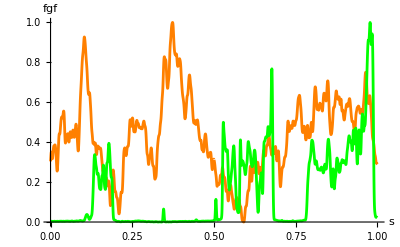
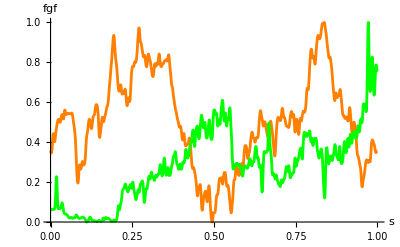
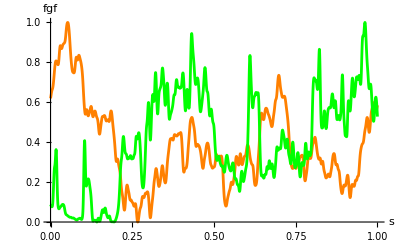
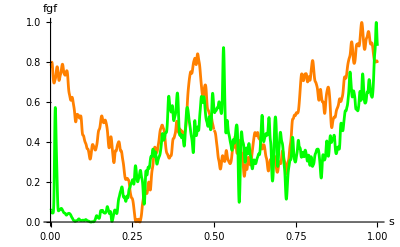
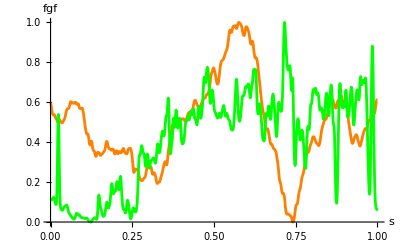
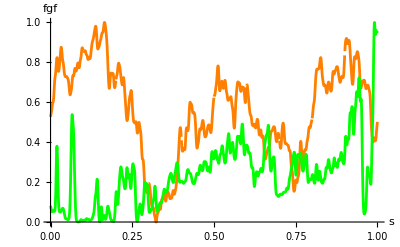
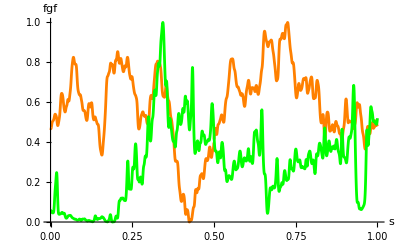
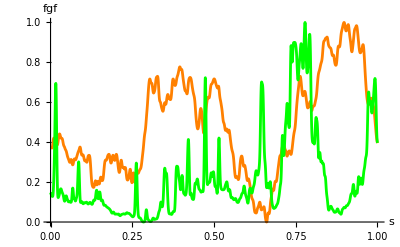

```mathematica
Show[{plotSyntheticData2[#],plotFGF[#]  }, PlotRange->All]&/@ Range[numOfFGFs]
```